## Sampling a sine wave

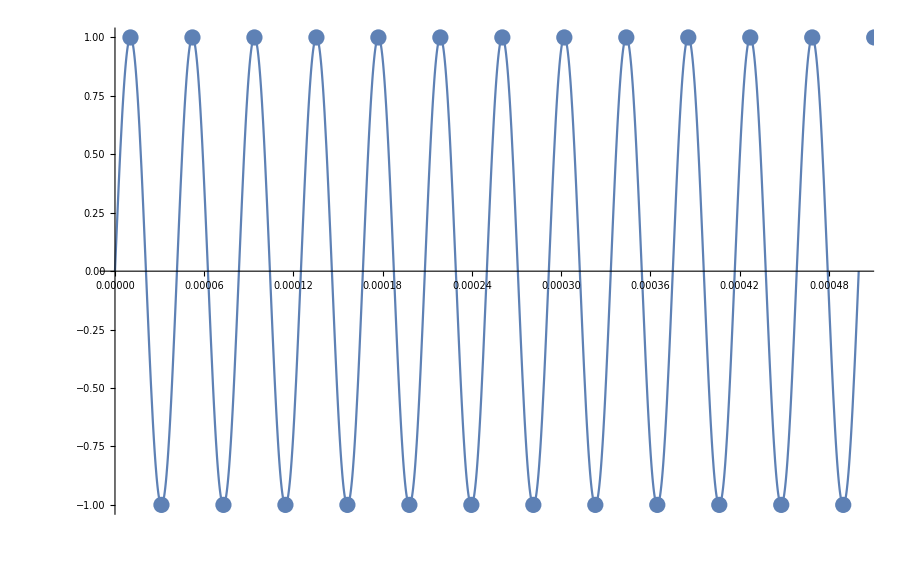

```mathematica
sineFreq[t_,f_]:=Sin[2π f t]
discreteSineFreq[n_,f_,sampleRate_]:=Sin[N[2π] f n / sampleRate]

plot1Time = 1/2000;
frequency1 = 24000;
sampleRate = 48000;
startTime = 0;
samplingShift = 1/2;
endTime = plot1Time+startTime;
continuousPlot = Plot[sineFreq[t,frequency1],{t,startTime,endTime}];
discreteData = Table[discreteSineFreq[n + samplingShift,frequency1,sampleRate],{n,Ceiling[startTime*sampleRate],Floor[endTime*sampleRate]}];
discretePlot = ListPlot[discreteData,DataRange->(samplingShift/sampleRate)+{Ceiling[startTime*sampleRate]/sampleRate,Floor[endTime*sampleRate]/sampleRate}];
Show[continuousPlot,discretePlot]
```

```mathematica
Manipulate[continuousPlot = Plot[sineFreq[t,audioFrequency],{t,startTime,endTime}];
discreteData = Table[discreteSineFreq[n + samplingShift,audioFrequency,sampleRate],{n,Ceiling[startTime*sampleRate],Floor[endTime*sampleRate]}];
discretePlot = ListPlot[discreteData,DataRange->(samplingShift/sampleRate)+{Ceiling[startTime*sampleRate]/sampleRate,Floor[endTime*sampleRate]/sampleRate}];
discreteLinePlot = ListLinePlot[discreteData,DataRange->(samplingShift/sampleRate)+{Ceiling[startTime*sampleRate]/sampleRate,Floor[endTime*sampleRate]/sampleRate},PlotStyle->Opacity[0.5]];
Show[continuousPlot,discreteLinePlot,discretePlot],{{samplingShift,1/2},0,1},{audioFrequency,2000,24000}]
```

## The Sinc function

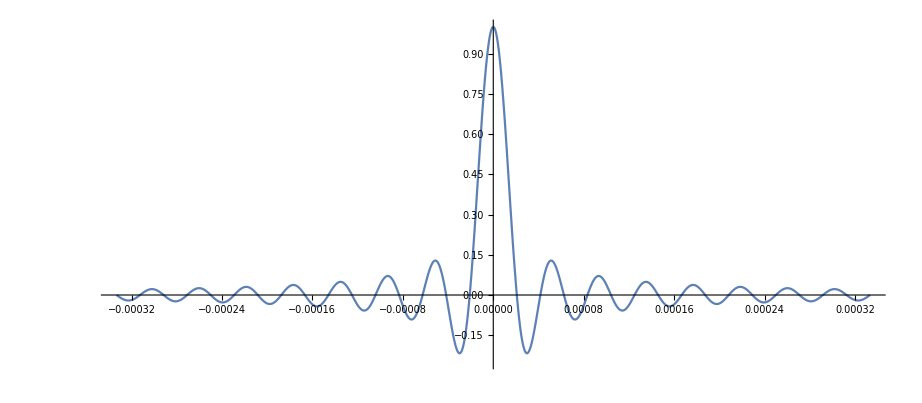

```mathematica
SincW[t_,W_]:=Sin[π (2 W t)]/(π(2 W t))
sincWidthSeconds = 1/3000;
Plot[SincW[t,24000],{t,-sincWidthSeconds,sincWidthSeconds},PlotRange->{-0.25,1}, AspectRatio->7/16]
```

## Reconstructing the continuous function from a sum of Sinc functions

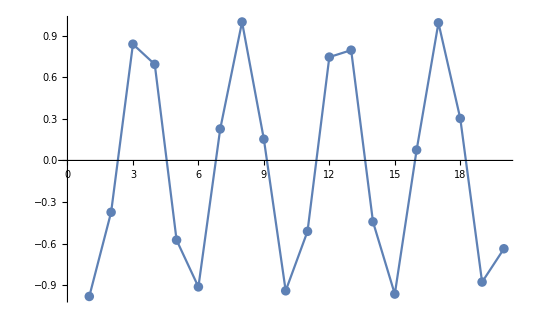

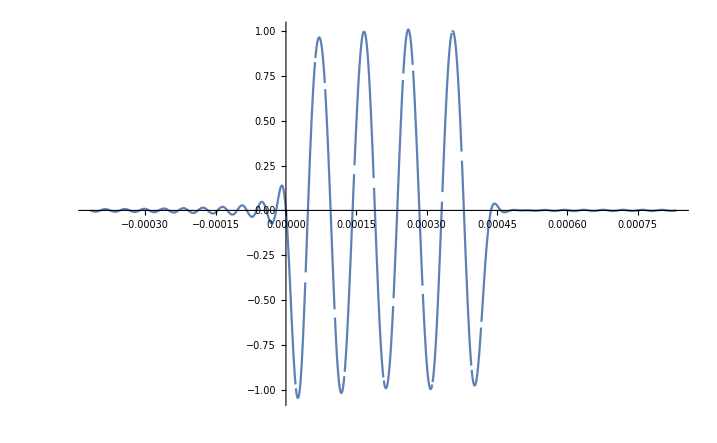

```mathematica
shiftedSinc[t_,n_,W_]:=SincW[t-n/(2W),W]
sincReconstruct[samples_,t_,W_]:=Total[Table[samples[[n]]shiftedSinc[t,n,W],{n,1,Length[samples]}]];
inputLength =20;
inputSamples =Range[inputLength]/inputLength; 
inputSamples = Table[Sin[1.1122π 5 n],{n,1,inputLength}];
Show[ListPlot[inputSamples],ListLinePlot[inputSamples]]
Plot[sincReconstruct[inputSamples,t,24000],{t,0 - inputLength/48000 , 2inputLength/48000},PlotRange->All]
```

```mathematica
20000*4
```

```mathematica
80000
96000
```

80000

192000